```mathematica
data=Join[
Import["C:\\Users\\Ye Lab\\Desktop\\Cal\\current_fpga\\dac_lower_drive\\board1.csv","Table"],
Import["C:\\Users\\Ye Lab\\Desktop\\Cal\\current_fpga\\dac_lower_drive\\board2.csv","Table"][[All,2;;]],
Import["C:\\Users\\Ye Lab\\Desktop\\Cal\\current_fpga\\dac_lower_drive\\board3.csv","Table"][[All,2;;]],
2];
freqs=data[[All,1]];
flat=data[[All,2;;All;;2]];
ramp=data[[All,3;;All;;2]];labels=Table[StringForm["DAC``",i],{i,24,47}];
```

```mathematica
IntegrateFFT[f_,y_,minfreq_,maxfreq_]:=Module[{fft},
fft=Interpolation[Transpose@{f,y},InterpolationOrder->1];
√NIntegrate[fft[x]^2,{x,minfreq,maxfreq}]
]
fmin=31.25;
fmax=100000;
```

```mathematica
floor = Import["C:\\Users\\Ye Lab\\Desktop\\Cal\\current_fpga\\dac_lower_drive\\noise_floor.csv","Table"];
floorInt=IntegrateFFT[floor[[All,1]],floor[[All,2]],fmin,fmax];
10^6 floorInt
```

1.80147

```mathematica
flatInt=Map[IntegrateFFT[freqs,#,fmin,fmax]&,Transpose@flat];
rampInt=Map[IntegrateFFT[freqs,#,fmin,fmax]&,Transpose@ramp];
```

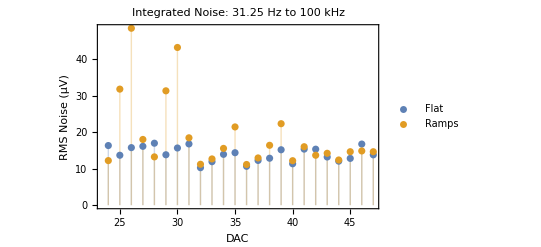

```mathematica
DACs=Table[x,{x,24,47}];
ListPlot[{Transpose@{DACs,10^6 flatInt},Transpose@{DACs,10^6 rampInt}},Frame->True,FrameLabel->{"DAC","RMS Noise (μV)"},
PlotLabel->"Integrated Noise: 31.25 Hz to 100 kHz",Filling->Bottom,
PlotLegends->Placed[PointLegend[{"Flat","Ramps"}],{0.85,0.85}],
PlotRange->All
]
```

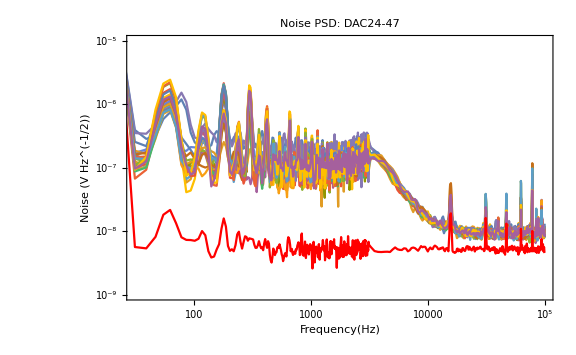

```mathematica
flatPlot=Map[Transpose@{freqs,#}&,Transpose@flat];
Show[
ListLogLogPlot[flatPlot,Joined->True,ImageSize->Large,Frame->True,PlotRange->{{fmin,fmax},{10^-9,10^-5}},FrameLabel->{"Frequency(Hz)","Noise (V Hz^(-1/2))"}],
ListLogLogPlot[floor,Joined->True,PlotStyle->Red],PlotLabel->"Noise PSD: DAC24-47"]
```